## Import astro

/Users/cmccabe/Google Drive/DarkSphere/AtomicCalcs/Plots/Scattering/Methane

/Users/cmccabe

InterpolatingFunction[…]

2.62585×10^-10

0.

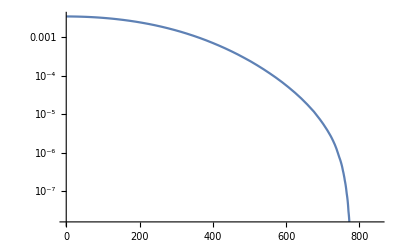

```mathematica
SetDirectory[NotebookDirectory[]]
Lgvmin=Import["gvmin_round.dat"];
ResetDirectory[]
fgvmin=Interpolation[Lgvmin,InterpolationOrder->1]
fgvmin[779]
fgvmin[780]

LogPlot[fgvmin[vmin],{vmin,0,850}]
```

## Import fion

/Users/cmccabe/Google Drive/DarkSphere/AtomicCalcs/Plots/molDM-main/Methane/Formfactor_Coulomb

/Users/cmccabe

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

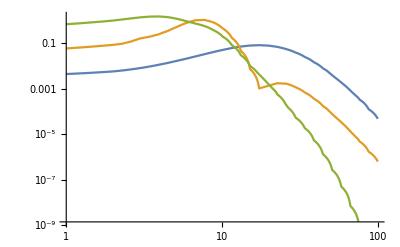

```mathematica
(*set path to form factor files*)
SetDirectory[NotebookDirectory[]<>"../../molDM-main/Methane/Formfactor_Coulomb"]
(*set path to form factor files*)

L1a=Import["CH4_1a_grid_PW_largeQ.dat"];
L2a=Import["CH4_2a_grid_PW_largeQ.dat"];
L1t=Import["CH4_1t_grid_PW_largeQ.dat"];
ResetDirectory[]

f1a=Interpolation[L1a,InterpolationOrder->1]
f2a=Interpolation[L2a,InterpolationOrder->1]
f1t=Interpolation[L1t,InterpolationOrder->1]

LogLogPlot[{f1a[qx,0.02],f2a[qx,0.02],f1t[qx,0.02]},{qx,1,100}]
```

## Parameters

```mathematica
Params1a=Association[
wnl->2,
Inl->290.8,
fionnl->f1a
];

Params2a=Association[
wnl->2,
Inl->22.9,
fionnl->f2a
];

Params1t=Association[
wnl->6,
Inl->13.6,
fionnl->f1t
];
```

## Rate calculation: FDM = 1

σe40 is the cross section relative to 10^-40 cm^2

#### dR/dE calculation: FDM = 1

```mathematica
TdRdE[mDMMeV0_,MNGeV0_,σe40_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

ρ=0.3;(*GeV cm^-3*)
σe=10^-40 σe40a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=779;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=  ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM=1

```mathematica
TdRETotal[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ1a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1t],InterpolationOrder->1];

Ftot[x_]:=fσ1a[x]+fσ2a[x]+fσ1t[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
ACH4=16.04;
MNGeV=ACH4 .931494; (*GeV*)
σ1=1; (*10^-40cm^2 cross section*)

TR30MeV=TdRETotal[30,MNGeV,σ1];
TR300MeV=TdRETotal[300,MNGeV,σ1];
TR1000MeV=TdRETotal[1000,MNGeV,σ1];

SetDirectory[NotebookDirectory[]];
Export["dRdE_CH4_30MeV.dat",TR30MeV]
Export["dRdE_CH4_300MeV.dat",TR300MeV]
Export["dRdE_CH4_1000MeV.dat",TR1000MeV]
ResetDirectory[];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {11.61093648190320237745254416950047016143798828125}. NIntegrate obtained 0.836865 and 7.42635×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {13.2662211620974}. NIntegrate obtained 0.831919 and 0.0000138444 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {15.1737711617091}. NIntegrate obtained 0.826769 and 0.0000122056 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {172.301337116417}. NIntegrate obtained 0.000150959 and 8.6024×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {172.321204562936}. NIntegrate obtained 0.00015079 and 1.21416×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {172.342009030721}. NIntegrate obtained 0.000150611 and 1.51161×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {214.738666043133}. NIntegrate obtained -0.00158239 and 1.31007×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {214.756892349371}. NIntegrate obtained -0.0015827 and 1.1336×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {173.49661919963}. NIntegrate obtained -0.001583 and 1.52202×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dRdE_CH4_30MeV.dat

dRdE_CH4_300MeV.dat

dRdE_CH4_1000MeV.dat

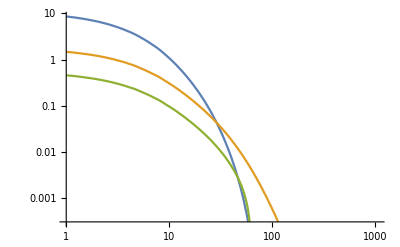

```mathematica
(*convert x-axis to eV*)
TR30MeV[[All,1]]=10^3 TR30MeV[[All,1]];
TR300MeV[[All,1]]=10^3 TR300MeV[[All,1]];
TR1000MeV[[All,1]]=10^3 TR1000MeV[[All,1]];


Show[ListLogLogPlot[{TR30MeV,TR300MeV,TR1000MeV},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```

## Rate calculation: FDM = (alpha me / q)^2

σe37 is the cross section relative to 10^-37 cm^2

#### dR/dE calculation: FDM = (alpha me / q)^2

```mathematica
TdRdElightmed[mDMMeV0_,MNGeV0_,σe37_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

αEM=1/137.04;
ρ=0.3;(*GeV cm^-3*)
σe=10^-37 σe37a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
mekeV=1000. meMeV;(*keV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=779;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

FDM[qkeV_]:=(αEM mekeV/qkeV)^2;

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=   FDM[qkeV]^2ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM = (alpha me / q)^2

```mathematica
TdRETotallightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ1a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1t],InterpolationOrder->1];

Ftot[x_]:=fσ1a[x]+fσ2a[x]+fσ1t[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
ACH4=16.04;
MNGeV=ACH4 .931494; (*GeV*)
σ1=1; (*10^-37cm^2 cross section*)

TR30MeVlightmed=TdRETotallightmed[30,MNGeV,σ1];
TR300MeVlightmed=TdRETotallightmed[300,MNGeV,σ1];
TR1000MeVlightmed=TdRETotallightmed[1000,MNGeV,σ1];

SetDirectory[NotebookDirectory[]];
Export["dRdE_CH4_30MeV_lightmed.dat",TR30MeVlightmed]
Export["dRdE_CH4_300MeV_lightmed.dat",TR300MeVlightmed]
Export["dRdE_CH4_1000MeV_lightmed.dat",TR1000MeVlightmed]
ResetDirectory[];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {11.61093648190320237745254416950047016143798828125}. NIntegrate obtained 0.863957 and 0.0000491643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {13.266221162097407759716816144646145403385162353515625}. NIntegrate obtained 0.847437 and 0.0000591083 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {15.1737711617090607063573770574294030666351318359375}. NIntegrate obtained 0.830395 and 0.0000410161 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {172.301337116417}. NIntegrate obtained 2.69919×10^-8 and 2.55284×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {172.321204562936}. NIntegrate obtained 2.69464×10^-8 and 2.82733×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {172.342009030721}. NIntegrate obtained 2.68983×10^-8 and 2.73049×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {173.4586608271572600870058522559702396392822265625}. NIntegrate obtained 2.37245×10^-8 and 1.14022×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {173.4772030044109811797170550562441349029541015625}. NIntegrate obtained 2.3689×10^-8 and 1.19434×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {173.4966191996295350463697104714810848236083984375}. NIntegrate obtained 2.36514×10^-8 and 1.25107×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dRdE_CH4_30MeV_lightmed.dat

dRdE_CH4_300MeV_lightmed.dat

dRdE_CH4_1000MeV_lightmed.dat

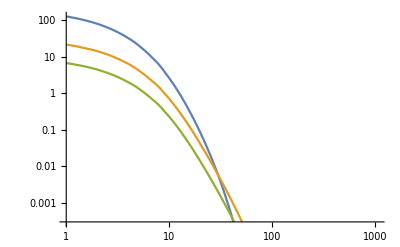

```mathematica
(*convert x-axis to eV*)
TR30MeVlightmed[[All,1]]=10^3 TR30MeVlightmed[[All,1]];
TR300MeVlightmed[[All,1]]=10^3 TR300MeVlightmed[[All,1]];
TR1000MeVlightmed[[All,1]]=10^3 TR1000MeVlightmed[[All,1]];


Show[ListLogLogPlot[{TR30MeVlightmed,TR300MeVlightmed,TR1000MeVlightmed},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```